-0.316228

{2 π ((6. t x[t] (-0.346+0.066 x[t]^2+0.13 x[t]^4-1.2 x[t]^6+x[t]^8-0.025 y[t]+0.666667 y[t]^2+0.00833333 y[t]^3-0.333333 y[t]^4))/((0.1+x[t]^2)^2)-x'[t]-t x''[t])==0,2 π ((4. t (0.01875-1. y[t]-0.01875 y[t]^2+y[t]^3))/(0.1+x[t]^2)-y'[t]-t y''[t])==0}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: There are significant errors {0.0000611094, 1.11022×10^-16, -0.0883107, 6.93934×10^-12} in the boundary value residuals. Returning the best solution found.

5.57901

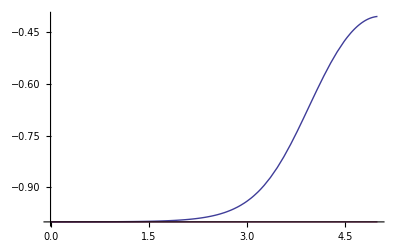

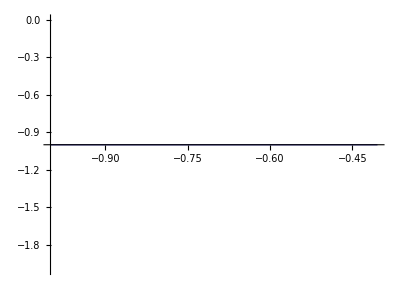

```mathematica
Needs["VariationalMethods`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
gamma=0.1;
delta1=0.1;
delta2=0.1;
tmin=0.0001;
tmax=5;
V[x[t_],y[t_]]:=(x[t]^2-1)^2(x[t]^2-delta1)+((y[t]^2-1)^2-(delta2(y[t]-2)(y[t]+1)^2)/4)/(x[t]^2+gamma);
U[x_,y_]:=(x^2-1)^2(x^2-delta1)+((y^2-1)^2-delta2(y-2)(y+1)^2/4)/(x^2+gamma);
ftn=2*Pi*t*(1/2(D[x[t],t]^2+D[y[t],t]^2)+V[x[t],y[t]]); (* Le Lagrangien *)
Veff[x_]:=U[x,-1];
x0=x/.FindRoot[Veff[x]==U[-1,-1],{x,-0.2}]
(*x1=x/.FindRoot[Veff[x]==U[-1,-1],{x,0.2}]*)
sln=EulerEquations[ftn,{x[t],y[t]},t]
solution=NDSolve[{sln,x[tmin]==-1,y[tmin]==-1,x[tmax]==x0,y[tmax]==-1},{x[t],y[t]},{t,tmin,tmax},Method->{"Shooting","StartingInitialConditions"->{x[tmin]==-1,x'[tmin]==0,y[tmin]==-1,y'[tmin]==0}}];
psi[t_]=x[t]/.solution[[1,1]];
phi[t_]=y[t]/.solution[[1,2]];
NIntegrate[2*Pi*t(1/2(D[psi[t],t]^2+D[phi[t],t]^2)+((psi[t]^2-1)^2(psi[t]^2-delta1)+((phi[t]^2-1)^2-delta2(phi[t]-2)(phi[t]+1)^2/4)/(psi[t]^2+gamma))),{t,tmin,tmax}]
(*solution2=NDSolve[{sln,x[tmin]==-1,y[tmin]==-1,x[tmax]==x1,y[tmax]==-1},{x[t],y[t]},{t,tmin,tmax}];
ksi[t_]=x[t]/.solution2[[1,1]];
khi[t_]=y[t]/.solution2[[1,2]];*)
Plot[{psi[t],phi[t]},{t,tmin,tmax},PlotRange->All]
(*Plot[{ksi[t],khi[t]},{t,tmin,tmax}]*)
ParametricPlot[{psi[t],phi[t]},{t,tmin,tmax},PlotRange->All]
(*NIntegrate[t(1/2(D[ksi[t],t]^2+D[khi[t],t]^2)+((ksi[t]^2-1)^2(ksi[t]^2-delta1)+((khi[t]^2-1)^2-delta2(khi[t]-2)(khi[t]+1)^2/4)/(ksi[t]^2+gamma))),{t,tmin,tmax}]*)
```